## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeNodes[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]],Automatic,0];
Union@adjNam[[All;;-2,1,1]]
];
```

```mathematica
Clear[calcRank];
calcRank[net_,type_,alpha_]:=calcRank[net,type,alpha]=Module[{d,s,vv,sg,ng,temp,maxRank,centrality,comps},
comps=ConnectedComponents[net[[2]]];
sg=Subgraph[net[[2]],comps[[1]]];
centrality=ConstantArray[0,VertexCount@net[[2]]];

Switch[type,
"d",d=VertexDegree[sg];s=Total@WeightedAdjacencyMatrix[sg];centrality[[VertexList[sg]]]=Switch[alpha,0,d,1,s,_,(If[#==0,0,#^(1-alpha)]&/@d)s^alpha]; (* following: Opsahl et al. 2010*),
"e",{vv}=Eigenvectors[1.Normal@If[alpha==0,AdjacencyMatrix[sg],WeightedAdjacencyMatrix[sg]],1];
centrality[[VertexList[sg]]]=Normalize[Abs[vv],Total];,
"b",ng=Graph[VertexList[net[[2]]],{Null,AdjacencyMatrix[net[[2]]]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[net[[2]],EdgeWeight]^-alpha];centrality=BetweennessCentrality[ng];,
"c",ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-alpha];
centrality[[VertexList[sg]]]=ClosenessCentrality[ng];
];

temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1]
];
cent2rank[centrality_]:=Module[{temp,maxRank},
temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1];
temp[[All,2]]
];
```

```mathematica
(* Adapted from:
Zand,M.S.,Wang,J.,Hilchey,S.,2015. Graphical Representation of Proximity Measures for Multidimensional Data.Math.J.17.
*)

mdsSVD[data_,dimensions_:2]:=Module[
{hmat, len, zeromeanData, uu,ww,vv},

{len=Length@data;
hmat=IdentityMatrix[len]-1/len;
zeromeanData=-hmat.N[data^2].hmat/2;
{uu,ww,vv}=SingularValueDecomposition[zeromeanData,dimensions]
}
][[1]]

classicalMDS[Dm_,dim_:2]:=
Module[{Idm,oneM,A,scale,J,Bm,Em,DmS,Ev,dMTX,EmM,coordX},{
DmS=Dm^2;
Idm=IdentityMatrix[Length[Dm]];
oneM=ConstantArray[1,Dimensions[Dm]];
scale=Length[Dm];
J=Idm-1./scale oneM;
Bm=-0.5 J.DmS.J;
Em=Eigenvectors[Bm,dim];
Ev=Eigenvalues[Bm,dim];
dMTX=DiagonalMatrix[Ev];
EmM=Transpose[Em];
coordX=EmM.√dMTX}][[1]]

metricMDS[dmT_,method_:{"DifferentialEvolution","SearchPoints"-> 30},precGoal_:5,accurGoal_:4,itr_:100]:=
Module[{m,n,Y,mY,stress,minVar,minSol,stval,sr},
{{m,n}={Length[dmT],2};

Y=Array[sr,{Length[dmT],2}];
minVar=Flatten[Y];

mY=Table[Sqrt[(Y[[i,1]]-Y[[j,1]])^2+(Y[[i,2]]-Y[[j,2]])^2],{i,m},{j,m}];
stress=Total[Table[(dmT[[i,j]]-mY[[i,j]])^2,{i,m},{j,m}],2];

minSol=NMinimize[stress,minVar,Method->method,PrecisionGoal-> precGoal,AccuracyGoal->accurGoal,MaxIterations->itr];
Y/.minSol[[2]]

}][[1]]
```

```mathematica
myOrdering[a_]:=GatherBy[Ordering@a,a[[#]]&];

simVR[va_,vb_,ca_,cb_]:=Module[{ra,rb,sum,norm,q,qL,qK,qM,x,y,posa,posb,temp,tempx,tempy},
ra=Flatten[ConstantArray[1.Mean[#],Length@#]&/@myOrdering[ca]];
rb=Flatten[ConstantArray[1.Mean[#],Length@#]&/@myOrdering[cb]];

(* compute the difference of graphs centralities *)
sum=Total@Flatten[Table[
posa=Position[va,i][[1,1]];
posb=Position[vb,i][[1,1]];
{(ca[[posa]]+cb[[posb]])/2(ra[[posa]]-rb[[posb]])^2}
,{i,Intersection[va,vb]}]~Join~
Table[
posa=Position[va,i][[1,1]];
{ca[[posa]](ra[[posa]]-Length@vb-1)^2}
,{i,Complement[va,vb]}]~Join~
Table[
posb=Position[vb,i][[1,1]];
{cb[[posb]](rb[[posb]]-Length@va-1)^2}
,{i,Complement[vb,va]}]];

(* Find the greedy maximum *)
qK=Table[posa=Position[va,i][[1,1]];posb=Position[vb,i][[1,1]];
(ca[[posa]]+cb[[posb]])/2,{i,Intersection[va,vb]}];
qL=Table[posa=Position[va,i][[1,1]];
ca[[posa]],{i,Complement[va,vb]}];
qM=Table[posb=Position[vb,i][[1,1]];
cb[[posb]],{i,Complement[vb,va]}];

qK=Sort[qK]; qL=Sort[qL]; qM=Sort[qM];
x=If[Length@Union@ra==1,ra,Sort[ra]];y =If[Length@Union@rb==1,rb,Sort[rb]];

norm=0;
While[Length@x>0||Length@y>0,
temp={Max[qK](Min@x-Max@y)^2,
tempx=Max[qL](x-Length@vb-1)^2;Max[tempx],
tempy=Max[qM](y-Length@va-1)^2;Max[tempy],
Max[qK](Max@x-Min@y)^2};
Switch[Position[temp,Max[temp/.Indeterminate->0]][[1,1]],
1,qK=Drop[qK,-1];x=Drop[x,1];y=Drop[y,-1];,
2,qL=Drop[qL,-1];x=Delete[x,Position[tempx,Max@tempx][[1]]];,
3,qM=Drop[qM,-1];y=Delete[y,Position[tempy,Max@tempy][[1]]];,
4,qK=Drop[qK,-1];x=Drop[x,-1];y=Drop[y,1];
];
norm=norm+Max[temp/.Indeterminate->0]
];

1-sum/norm
]
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
(* This one takes some time *)
nets=ParallelTable[makeNet[year,year],{year,yearList}];
```

### Graphics

```mathematica
marker1=Graphics[{EdgeForm[Directive[Thick,RGBColor[0,0,0],Opacity[1]]],White,Disk[]},ImageSize->14];
marker2=Graphics[{EdgeForm[Directive[Thick,RGBColor[1,0,0],Opacity[1]]],RGBColor[1,1,1],Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->15];
marker3=Graphics[{RGBColor[0,0,1],Polygon[{{1/2,0},{0,1/2},{1/2,1},{1,1/2}}]},ImageSize->15];
```

```mathematica
(* Overlays for the timeline figures *)
shade=ListPlot[Transpose@{{1248+7/12,1249+8/12},ConstantArray[ee,2]},Joined->True,Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]]];
line=ListPlot[{{1230,ee},{1253,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
line1=ListPlot[{{1230+0.5,ee},{1253+0.5,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
```

```mathematica
(* https://mathematica.stackexchange.com/questions/13547/how-do-i-add-arrowheads-to-circular-arcs *)
ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Directive[GrayLevel[.3],Arrowheads[{{-0.05,0},{0.05,1}}]]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]
```

## Result 1

### Subgraph similarity

```mathematica
sgsim1=ParallelTable[
a=nets[[i-1]];
b=nets[[i]];
va=Union@Flatten@a[[1,All;;-2,1]];
vb=Union@Flatten@b[[1,All;;-2,1]];
{yearList[[i]],1.-(Length@Intersection[va,vb])/Max[Length@va,Length@vb]}
,{i,2,Length@yearList}];
sgsim2=ParallelTable[
a=nets[[i-1]];
b=nets[[i]];
va=a[[1,All;;-2,1]];
vb=b[[1,All;;-2,1]];
{yearList[[i]],1.-(Length@Intersection[va,vb])/Max[Length@va,Length@vb]}
,{i,2,Length@yearList}];
```

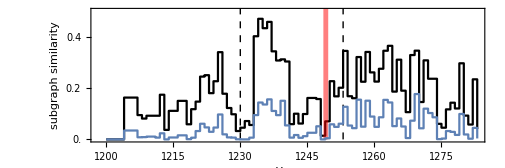

```mathematica
Show[{ListPlot[{#[[1]],1-#[[2]]}&/@sgsim1,Joined->True,InterpolationOrder->0,PlotStyle->Black,Frame->True,PlotRange->{0.,.5},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,0.5,0.1}]~Join~Table[{t,"",{0.005,0}},{t,0.05,1,0.1}],Table[{t,"",{0.01,0}},{t,0,0.5,0.1}]~Join~Table[{t,"",{0.005,0}},{t,0.05,1,0.1}]},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["subgraph similarity","Arial",14,Black]},ImageSize->505,AspectRatio->1/3],shade,line,ListPlot[{#[[1]],1-#[[2]]}&/@sgsim2,Joined->True,InterpolationOrder->0,PlotStyle->Automatic]}]
```

### MDS and SVD of graph similarity

```mathematica
sgsim3=ParallelTable[
a=nets[[i]];
va=Union@Flatten@a[[1,All;;-2,1]];
Table[
b=nets[[j]];
vb=Union@Flatten@b[[1,All;;-2,1]];
{yearList[[i]],yearList[[j]],1.-(Length@Intersection[va,vb])/Max[Length@va,Length@vb]}
,{j,i,Length@yearList}]
,{i,1,Length@yearList}];
sgsim3Mat=SparseArray[{#[[1]],#[[2]]}->#[[3]]&/@Flatten[sgsim3,1]];
```

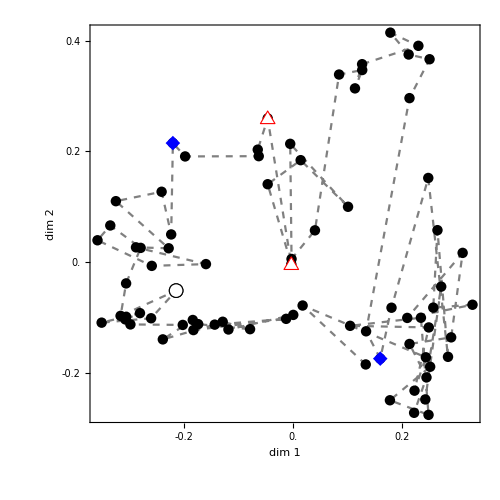

```mathematica
mdsRes=classicalMDS[sgsim3Mat[[yearList,yearList]]+Transpose[sgsim3Mat[[yearList,yearList]]]];
ticksL=Table[{i,ToString[i],{0.02,0}},{i,-0.4,0.4,0.2}]~Join~Table[{i,"",{0.01,0}},{i,-0.3,0.3,0.2}];
ticksR=Table[{i,"",{0.02,0}},{i,-0.4,0.4,0.2}]~Join~Table[{i,"",{0.01,0}},{i,-0.3,0.3,0.2}];
Show[
{
ListPlot[Tooltip[#[[2]],#[[1]]]&/@Transpose[{yearList,mdsRes}],Frame->True,Joined->True,Mesh->All,MeshStyle->{Black,PointSize[0.015]},PlotStyle->{Dashed,Gray},ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{ticksL,ticksR},{ticksL,ticksR}},FrameLabel->(Style[#,14,"Arial",Black]&/@{"dim 1","dim 2"})],
ListPlot[#+{0,0.002}&/@mdsRes[[{42,43}]],PlotMarkers->marker2],
ListPlot[mdsRes[[{60}]],PlotMarkers->marker1],
ListPlot[mdsRes[[{25,47}]],PlotMarkers->marker3]
},AspectRatio->1
]
```

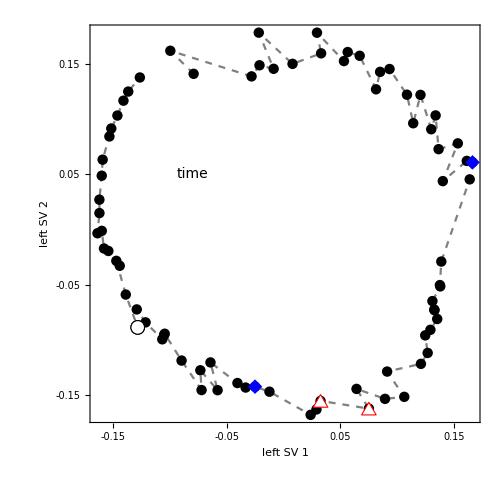

```mathematica
mdsRes=mdsSVD[sgsim3Mat[[yearList,yearList]](*+LowerTriangularize[ConstantArray[1.,{77,77}],-1]*)];
ticksL=Table[{i,ToString[i],{0.02,0}},{i,-0.15,0.15,0.1}]~Join~Table[{i,"",{0.01,0}},{i,-0.1,0.15,0.1}];
ticksR=Table[{i,"",{0.02,0}},{i,-0.15,0.15,0.1}]~Join~Table[{i,"",{0.01,0}},{i,-0.1,0.15,0.1}];
rdsAndAngls={{2,{5π/6,(8 π)/3}}};
directives=Directive[Black,Thick,Arrowheads[{{-0.05,0}(*,{0.05,1}*)}]];
Show[
{
ListPlot[Tooltip[#[[2]],#[[1]]]&/@Transpose[{yearList,mdsRes[[1]]}],Frame->True,Joined->True,Mesh->All,MeshStyle->{Black,PointSize[0.015]},PlotStyle->{Dashed,Gray},ImageSize->500,
Epilog->{Inset[arcsWArrows[rdsAndAngls,{directives}],{0,0},Automatic,0.25],Inset["time",{-0.08,0.05}]},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{ticksL,ticksR},{ticksL,ticksR}},FrameLabel->(Style[#,14,"Arial",Black]&/@{"left SV 1","left SV 2"})],
ListPlot[mdsRes[[1,{42,43}]],PlotMarkers->marker2],
ListPlot[mdsRes[[1,{60}]],PlotMarkers->marker1],
ListPlot[mdsRes[[1,{25,47}]],PlotMarkers->marker3]
},AspectRatio->1
]
```

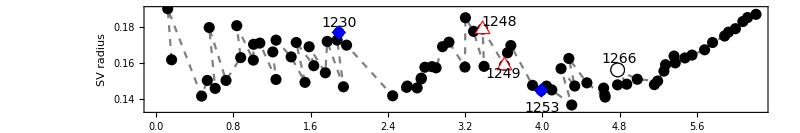

```mathematica
insets={Inset[1230,{1.9,0.182}],Inset[1248,{3.55,0.183}],Inset[1249,{3.6,.154}],(*Inset[1250,{-0.087,-0.0014}]*),Inset[1253,{4,.135}],Inset[1266,{4.8,0.162}]};
circle=Table[{2π-Mod[Which[mdsRes[[1,t,2]]>0&&mdsRes[[1,t,1]]>0,3π/2-ArcTan[mdsRes[[1,t,1]]/mdsRes[[1,t,2]]],
mdsRes[[1,t,2]]<0&&mdsRes[[1,t,1]]>0,π/2-ArcTan[mdsRes[[1,t,1]]/mdsRes[[1,t,2]]],mdsRes[[1,t,2]]<0&&mdsRes[[1,t,1]]<0,π/2-ArcTan[mdsRes[[1,t,1]]/mdsRes[[1,t,2]]],mdsRes[[1,t,2]]>0&&mdsRes[[1,t,1]]<0,3/2π-ArcTan[mdsRes[[1,t,1]]/mdsRes[[1,t,2]]]]+π/3.5,2π],Norm[mdsRes[[1,t]]]},{t,1,77}];
Show[
{
ListPlot[
Tooltip[#[[2]],#[[1]]]&/@Transpose[{yearList,circle}],Frame->True,Joined->True,Mesh->All,MeshStyle->{Black,PointSize[0.01]},PlotStyle->{Dashed,Gray},ImageSize->800,
Epilog->insets,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicksStyle->Directive[12,"Arial",Black](*,FrameTicks->None*),FrameLabel->(Style[#,14,"Arial",Black]&/@{"SV angle [rad]","SV radius"})],
ListPlot[#+{0.0,0.001}&/@circle[[{42,43}]],PlotMarkers->marker2(*PlotStyle->{PointSize[0.02],Red}*)],
ListPlot[circle[[{60}]],PlotMarkers->marker1(*PlotStyle->{PointSize[0.02],Red}*)],
ListPlot[circle[[{25,47}]],PlotMarkers->marker3](*,
ListPlot[circle[[60]],PlotStyle->{PointSize[0.02],Red}]*)
},AspectRatio->1/6
]
```

### Vertex ranking similarity (Papadimitriou et al., 2010)

```mathematica
funcDS=ParallelTable[
net=nets[[i]];
Association[
c->MapIndexed[Append[Association@Thread[{"c-1","d0","c0","e0",(*"b0",*)"d1","c1","e1",(*"b1",*)"d0.5","c0.5",(*"b0.5",*)"d1.5","c1.5"(*,"b1.5"*)}->#1],Association["name"->names[[#2[[1]]]]]]&,
Transpose@Table[
1.calcRank[net,i[[1]],i[[2]]][[All,2]]
,{i,{{"c",-1(*wrong*)},{"d",0(*degree*)},{"c",0(*unweighted*)},{"e",0(*unweighted*)},(*{"b",0},*){"d",1(*strength*)},{"c",1(*inverse*)},{"e",1(*weighted*)},(*{"b",1},*){"d",0.5},{"c",0.5},(*{"b",0.5},*){"d",1.5},{"c",1.5}(*,{"b",1.5}*)}}]
]
]
,{i,1,Length@yearList}];
funcDS=Dataset@funcDS;
```

```mathematica
(* This might take a while *)
sgsim4=ParallelTable[
a=nets[[i-1]];
b=nets[[i]];
va=Union@Flatten@a[[1,All;;-2,1]];
vb=Union@Flatten@b[[1,All;;-2,1]];
a=Subgraph[a[[2]],va];
b=Subgraph[b[[2]],vb];
orda=Ordering@Flatten[ConnectedComponents[a]];
ordb=Ordering@Flatten[ConnectedComponents[b]];
{yearList[[i]],Table[
ca=Flatten[Normal@funcDS[i-1,1,#,cc]&/@ConnectedComponents[a]][[orda]];
cb=Flatten[Normal@funcDS[i,1,#,cc]&/@ConnectedComponents[b]][[ordb]];
simVR[va,vb,ca,cb]
,{cc,{"c-1","d0","c0","e0",(*"b0",*)"d1","c1","e1",(*"b1",*)"d0.5","c0.5",(*"b0.5",*)"d1.5","c1.5"(*,"b1.5"*)}}]}
,{i,2,Length@yearList}];
```

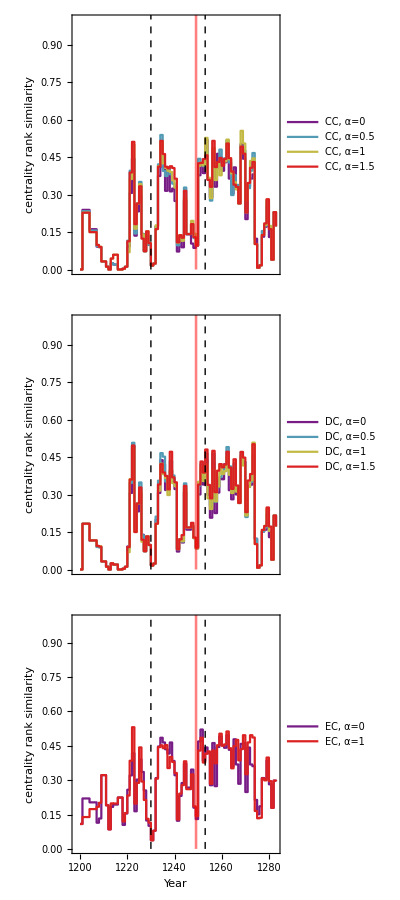

```mathematica
Grid@{{Show[{ListPlot[Transpose@{sgsim4[[All,1]],sgsim4[[All,2,#]]}&/@{(*1,*)3,9,6,11}(*{2,8,5,10}*),Joined->True,InterpolationOrder->0,PlotStyle->"Rainbow",Frame->True,PlotRange->{0,1.},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{None,Automatic}},FrameLabel->{(*Style["Year","Arial",12,Black]*)None,Style["centrality rank similarity","Arial",14,Black]},ImageSize->505,AspectRatio->1/3,PlotLegends->Placed[{(*"c-1",*)"CC, α=0","CC, α=0.5","CC, α=1","CC, α=1.5"},{0.12,0.6}]],shade,line}]},{
Show[{ListPlot[Transpose@{sgsim4[[All,1]],sgsim4[[All,2,#]]}&/@{2,8,5,10},Joined->True,InterpolationOrder->0,PlotStyle->"Rainbow",Frame->True,PlotRange->{0,1.},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{None,Automatic}},FrameLabel->{(*Style["Year","Arial",12,Black]*)None,Style["centrality rank similarity","Arial",14,Black]},ImageSize->505,AspectRatio->1/3,PlotLegends->Placed[{"DC, α=0","DC, α=0.5","DC, α=1","DC, α=1.5"},{0.12,0.6}]],shade,line}]},{
Show[{ListPlot[Transpose@{sgsim4[[All,1]],sgsim4[[All,2,#]]}&/@{4,7},Joined->True,InterpolationOrder->0,PlotStyle->"Rainbow",Frame->True,PlotRange->{0,1.},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["centrality rank similarity","Arial",14,Black]},ImageSize->505,AspectRatio->1/3,PlotLegends->Placed[{"EC, α=0","EC, α=1"},{0.12,0.6}]],shade,line}]}}
Show[{ListPlot[Transpose@{sgsim4[[All,1]],sgsim4[[All,2,#]]}&/@{2,3,4},Joined->True,InterpolationOrder->0,PlotStyle->"Rainbow",Frame->True,PlotRange->{0,1.},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["centrality rank similarity","Arial",14,Black]},ImageSize->505,AspectRatio->1/3,PlotLegends->{"d0","c0","e0"}],shade,line}]
```